```mathematica
ClearAll["Global`*"]
```

```mathematica
Kerr Orbit GR Project
Erik Tollerud 
June 14, 2007
```

```mathematica
Introduction/Technique
```

The Kerr geometry is described by a far more complicated metric than the Schwarzschild geometry or other relatively simple solutions to the Einstein equation. Hence, it seems reasonable that calculation of orbits in that geometry would require either exceedingly clever analytic techniques (which invariably will be somewhat limited), or numerical evaluation.  The aim of this project is to test the feasibility of the latter to compute free-fall orbits in the Kerr geometry.
The overall technique here is to compute the geodesic equation from the Christoffel symbols (with Mathematica doing all the algebraic leg work).  From this, differential equations will be fained that can be solved with the appropriate initial conditions. Results will be compared where possible to analytic examples, and the scalar product u·u will be monitored to see if it remains invarient under the numerical evaluation and integration. A final useful check is to examine the results in the case of the perihelion shift of Mercury.  It is expected that rotation on the scale of the sun will not noticeably perturb this precession, and we want to try to recover this result. 
(Note that the commands below load Mathematica packages necessary for the rest of this notebook.)

```mathematica
<<Graphics`
<<Graphics`Legend`
<<Graphics`ParametricPlot3D`
```

General::obspkg: "Graphics`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::obspkg: "Graphics`Legend`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::obspkg: "Graphics`ParametricPlot3D`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
Flat Spacetime Solution
```

As an initial "proof-of-concept", we'll try this method for the flat minkowski spacetime (η_αβ).  First we define the metric and compute its inverse (although trivial in this case, it illustrates the technique).

```mathematica
coords = {t,x,y,z}
n=Length[coords];
metric={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
metric//MatrixForm
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm
```

{t,x,y,z}

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Next, we solve for the Christoffel symbols following the technique in the "Christoffel Symbols and Geodesic Equation" Mathematica notebook from the textbook web site, by using the definitions of the symbols and Mathematica's algebraic skills.

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}]
```

{}

While the Christoffel symbols vanish for the Minkowski metric, in general this is not true, so we compute the Geodesic equation as though they were present.

```mathematica
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]u[j]u[k],{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[u[i]],"=",geodesic[[i]]},{i,1,n}]
TableForm[listgeodesic,TableSpacing->{2}]
```

d/dτ u[1] | = | 0
d/dτ u[2] | = | 0
d/dτ u[3] | = | 0
d/dτ u[4] | = | 0

And indeed, unsurprisingly, the result is the equation of motion for a particle subject to no forces at all.  We now use the mathematica differential equation solver to compute the spacetime coordinates as a function of proper time τ  given a particular set of initial spatial velocities, assuming we start at the origin. As we are interested in a particle orbit rather than a light ray, the final necessary equation is u·u=-1, which can be used to solve for the initial dt/dτ,giving t'^2=1+x'^2+y'^2+z'^2(where priming is differentiation with respect to τ)

```mathematica
ivs={1.1,0,0};
ics={0,0,0,0};
ivs=Join[{Sqrt[1+ivs.ivs]},ivs];
deqs=Join[Table[coords[[i]]''[τ]==geodesic[[i]],{i,1,n}],Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=DSolve[deqs,coords,τ]//Flatten;
vx=D[x[τ]/.soln,τ]/D[t[τ]/.soln,τ];
t==(t[τ]/.soln)
x==(x[τ]/.soln)
y==(y[τ]/.soln)
z==(z[τ]/.soln)
dx/dt==vx
γ==(1-vx^2)^(-1/2)
```

t==1.48661 τ

x==1.1 τ

y==0

z==0

dx/dt==0.73994

γ==1.48661

While it may seem incorrect to use an initial velocity of 1.1, the initial velocities are expressed as dx_i/dτ,which are not limited to speeds of 1 (e.g. c in units of c=1). Computing dx/dτ/dt/dτ gives the observed coordinate speed dx/dt, and indeed, this is less than 1. Furthermore, computing the special relativistic gamma using this velocity gives back the result same number as appears in the t(τ) equation, confirming that this technique is consistant with special relativity.

```mathematica
Kerr Geometry
```

Now we repeat the same steps, but this time with the Kerr Geometry using Boyer-Lindquist coordinates.  We begin by defining the metric  in terms of the parameters M, a,ρ and Δ, then find the inverse.

```mathematica
coords = {t,r,θ,ϕ}
n=Length[coords];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=-4 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm
```

{t,r,θ,ϕ}

(-1+(2 M r)/ρ | 0 | 0 | -(4 a M r Sin[θ]^2)/ρ
0 | ρ/Δ | 0 | 0
0 | 0 | ρ | 0
-(4 a M r Sin[θ]^2)/ρ | 0 | 0 | (Δ+(2 M r (a^2+r^2))/ρ) Sin[θ]^2)

(-(ρ (2 a^2 M r+2 M r^3+Δ ρ))/(2 a^2 M r (2 M r+ρ)-(2 M r-ρ) (2 M r^3+Δ ρ)-8 a^2 M^2 r^2 Cos[2 θ]) | 0 | 0 | (4 a M r ρ)/(-2 a^2 M r (2 M r+ρ)+(2 M r-ρ) (2 M r^3+Δ ρ)+8 a^2 M^2 r^2 Cos[2 θ])
0 | Δ/ρ | 0 | 0
0 | 0 | 1/ρ | 0
(4 a M r ρ)/(-2 a^2 M r (2 M r+ρ)+(2 M r-ρ) (2 M r^3+Δ ρ)+8 a^2 M^2 r^2 Cos[2 θ]) | 0 | 0 | (ρ (-2 M r+ρ) Csc[θ]^2)/(2 a^2 M r (2 M r+ρ)-(2 M r-ρ) (2 M r^3+Δ ρ)-8 a^2 M^2 r^2 Cos[2 θ]))

This inverse is already a mess, so we will first investigate the degenerate case of a→0 .

```mathematica
a=0;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
metric//MatrixForm
```

(-1+(2 M)/r | 0 | 0 | 0
0 | r^2/(-2 M r+r^2) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

This is clearly the form of the Schwarzschild metric, so we will briefly examine the dynamics here to provide results for comparison in the full-fledged Kerr geometry with non-zero a.

```mathematica
Schwarzschild Solutions
```

With the metric and its inverse in hand, we can compute the Christoffel symbols and geodesic equations in the same fashion as for Minkowski spacetime.

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
TableForm[listgeodesic,TableSpacing->{2}]
```

Γ[1, 2, 1] | -M/(2 M r-r^2)
Γ[2, 1, 1] | (M (-2 M+r))/r^3
Γ[2, 2, 2] | M/(2 M r-r^2)
Γ[2, 3, 3] | 2 M-r
Γ[2, 4, 4] | (2 M-r) Sin[θ]^2
Γ[3, 3, 2] | 1/r
Γ[3, 4, 4] | -Cos[θ] Sin[θ]
Γ[4, 4, 2] | 1/r
Γ[4, 4, 3] | Cot[θ]

d/dτ t' | = | (2 M r' t')/(2 M r-r^2)
d/dτ r' | = | (-M r^2 (r')^2+(-2 M+r)^2 (M (t')^2-r^3 ((θ')^2+Sin[θ]^2 (ϕ')^2)))/((2 M-r) r^3)
d/dτ θ' | = | -(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2
d/dτ ϕ' | = | -(2 (r'+r Cot[θ] θ') ϕ')/r

Now  we supply initial conditions and solve for the  coordinates parameterized in τ. Note that Mathematica cannot generate a general analytic solution using DSolve, so we resort to numerical the NDSolve by taking M=1.  Furthermore, to compute the initial dt/dτ, the  n·n=-1 equation is much more complicated, as the scalar product must be computed in the general tensor form g_αβ u^α u_β = -1. Mathematica can do this and solve for the resulting initial condition for dt/dτ. For simplicity's sake, this will be written as a function that can later be called for a set of initial conditions, implicitly using the variables defined as "coords","metric", and "geodesic".

```mathematica
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,{τ,0,maxτi}];
soln]
uinvar=-1;
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
udotu[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];
xα=xα/.τ->τval;uα=uα/.τ->τval;uα.((metric/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
coordlist[τin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

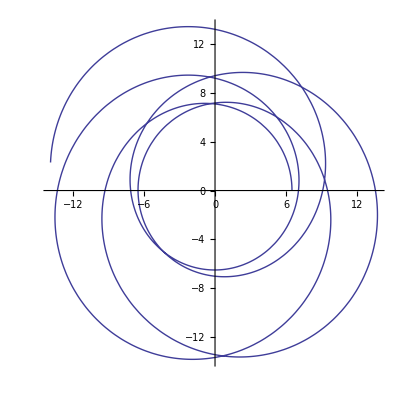

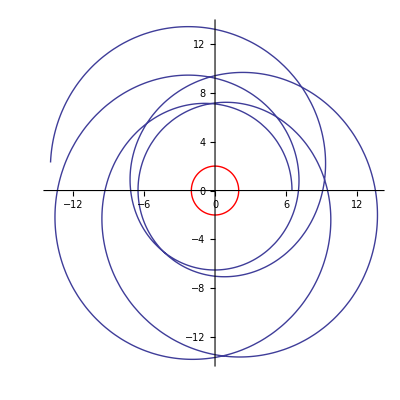

Final Coordinates:
t = 895.184
r = 14.0802
θ = 1.5708
ϕ = 28.1106

|  |  | u·u values
τ= | 0 | → | -1.
τ= | 150 | → | -1.
τ= | 300 | → | -1.
τ= | 450 | → | -1.
τ= | 600 | → | -1.
τ= | 750 | → | -1.

```mathematica
maxτ=750;
ivs={0,0,.088};
ics={0,6.5,π/2,0};
M=1;
soln=computeSoln[maxτ,ivs,ics];
Plot[Evaluate[Table[coords[[i]][τ]/.soln,{i,1,n}]],{τ,0,maxτ},PlotStyle->Table[Hue[(i-1)/n],{i,1,n}],PlotLegend->coords,LegendPosition->{1,-.35},AxesLabel->{"τ","Coordinate"}];
xyzsoln=sphslnToCartsln[soln];
horizpl=PolarPlot[2,{θ,0,2 Pi},PlotStyle->Hue[0],DisplayFunction->Identity];
ParametricPlot[Evaluate[{xyzsoln[[1]],xyzsoln[[2]]}//Flatten],{τ,0,maxτ},AspectRatio->1,DisplayFunction->Identity]
Show[%,horizpl,DisplayFunction->$DisplayFunction]
Join[{"Final Coordinates:"},coordlist[maxτ]]//TableForm
Join[{{"","","","u·u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

(the red circle is the horizon at r=2M) Here we see clear evidence of precession, as expected in the Schwarzschild metric close to the horizon.  Also of note is the modest time dilation for this orbit - while the proper time τ goes from 0 to 750, the coordinate time t extends up to ~870.  Also of note is the fact that u·u =-1 for the whole orbit.  This is a sign that the equations are properly solved and numerical errors are not significantly disrupting the orbit.

A different set of initial conditions helps understand what is occuring at the horizon. In Schwarzschild coordinates results there is a singularity at the horizon, and hence, numerical equation solving cannot cross the horizon. We can, however, see how the coordinate time t (which becomes the familiar time in the asymptotically flat spacetime at large r) changes.  As the particle falls radially in towards the horizon, its coordinate time is asymptotically increasing, so observers from the outside will never actually see it strike the horizon. At the point here, time dilation has already more doubled t with respect to τ (versus the last case, where even after a much longer τ, time dilation was only a factor of ~1.1)

One other important effect to be noted that became apparent from drawing these graphs for a variety of initial conditions is a transition at r0=  6 M.  within that radius, it was impossible to establish a stable circular orbit.  Some elliptical orbits showed relatively long terms stability, but if the orbit began inside a radius of 6M, even tuning the initial dϕ/dτ to 8 decimal places resulted in an eventual plunge to the horizon (as shown below).  Outside this radius, a circular  orbit was relatively easy to attain with only a few decimal place's tuning (see second figure for an example). This further shows that this technique is reproducing the analytically describable Schwarzschild geometry. (Note that the green circle here is r_ISCO=6 M)

One final point to note about the Schwarzschild geometry is the inherent spherical symmetry. These two plots were made with initial velocities in all three spatial coordinates, yet it is clear that the orbit is still in a plane (although it is now tipped with respect to the z-axis).  This is not expected in the general Kerr geometry that has a preferred rotational axis.

```mathematica
maxτ=2000;
ivs={-.08,.035,.0359};
ics={0,10,π/4,.2};
xyzsoln=sphslnToCartsln[computeSoln[maxτ,ivs,ics]];
sphhoriz=SphericalPlot3D[{2,EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity];
angle=ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},DisplayFunction->Identity];
edge=ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},ViewPoint->{2,1.6,0},DisplayFunction->Identity];
Show[angle,sphhoriz,DisplayFunction->$DisplayFunction,PlotRange->{{-30,30},{-30,30},{-30,30}}]
Show[edge,sphhoriz,DisplayFunction->$DisplayFunction,PlotRange->{{-30,30},{-30,30},{-30,30}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
General Kerr Solutions
```

Now we attempt to solve for the more general case of a≠0. First we compute the geodesic in terms of the parameters M,a,ρ, and Δ.

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
TableForm[Partition[DeleteCases[Flatten[listgeodesic],Null],2],TableSpacing->{2,2}]
```

Γ[1, 2, 1] | -(M (a^2-2 r^2+a^2 Cos[2 θ]) (a^4+2 r^4+3 a^2 r (-2 M+r)+a^2 (a^2+r (6 M+r)) Cos[2 θ]))/(4 (r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[1, 3, 1] | -(a^2 M r Cos[θ] (a^4+2 r^3 (-8 M+r)+a^2 r (-14 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ]) Sin[θ])/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[1, 4, 2] | (2 a M (-r^2 (a^2+3 r^2)+a^2 (a^2-r^2) Cos[θ]^2) Sin[θ]^2)/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[1, 4, 3] | (4 a^3 M r (a^2+r (-2 M+r)) Cos[θ] Sin[θ]^3)/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[2, 1, 1] | -(M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
Γ[2, 2, 2] | (r (a^2-M r)+a^2 (M-r) Cos[θ]^2)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2))
Γ[2, 3, 2] | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ[2, 3, 3] | -(r (a^2+r (-2 M+r)))/(r^2+a^2 Cos[θ]^2)
Γ[2, 4, 1] | (2 a M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ[2, 4, 4] | ((a^2+r (-2 M+r)) (a^2 M r^2-r^5-a^2 (a^2 M+r^2 (M+2 r)) Cos[θ]^2+a^4 (M-r) Cos[θ]^4) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 1, 1] | -(2 a^2 M r Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 2, 2] | (a^2 Cos[θ] Sin[θ])/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2))
Γ[3, 3, 2] | r/(r^2+a^2 Cos[θ]^2)
Γ[3, 3, 3] | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ[3, 4, 1] | (2 a M r (a^2+r^2) Sin[2 θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ[3, 4, 4] | -(Cos[θ] Sin[θ] (a^2-2 M r+r^2+(2 M r (a^2+r^2))/(r^2+a^2 Cos[θ]^2)+(2 a^2 M r (a^2+r^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^2)))/(r^2+a^2 Cos[θ]^2)
Γ[4, 2, 1] | (2 a M (r^2-a^2 Cos[θ]^2))/(2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))
Γ[4, 3, 1] | -(2 a M r (a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]) Cot[θ])/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[4, 4, 2] | (2 a^2 M^2 r^3-a^2 M r^4-2 M r^6+r^7-a^2 r (2 a^2 M^2+r^2 (2 M^2+3 M r-3 r^2)) Cos[θ]^2+a^4 (a^2 M+r (2 M^2-2 M r+3 r^2)) Cos[θ]^4-a^6 (M-r) Cos[θ]^6-8 a^2 M^2 r^3 Sin[θ]^2+2 a^4 M^2 r Sin[2 θ]^2)/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))
Γ[4, 4, 3] | (Cos[θ] (a^2 r^2 (a^2 (-4 M^2+3 r^2)+r^2 (4 M^2-6 M r+3 r^2)) Cos[θ] Cot[θ]+a^4 r^2 (3 a^2+4 M^2-6 M r+3 r^2) Cos[θ]^3 Cot[θ]+a^6 (a^2+r (-2 M+r)) Cos[θ]^5 Cot[θ]+2 a^4 M r (a^2+r (8 M+r)) Cos[θ]^2 Sin[θ]+r^2 (-(2 M-r) r^2 (r^3+a^2 (2 M+r)) Csc[θ]+2 a^2 M (a^2 (2 M+r)+r^2 (6 M+r)-4 a^2 M Cos[2 θ]) Sin[θ])))/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))

d/dτ t' | =
(M (a^2 r θ' (2 (a^4+2 r^3 (-8 M+r)+a^2 r (-14 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ]) Sin[2 θ] t'-8 a (a^2+r (-2 M+r)) Cos[θ] (a^2+2 r^2+a^2 Cos[2 θ]) Sin[θ]^3 ϕ')+r' ((a^2-2 r^2+a^2 Cos[2 θ]) (a^4+2 r^4+3 a^2 r (-2 M+r)+a^2 (a^2+r (6 M+r)) Cos[2 θ]) t'+8 a ((r^4 (a^2+3 r^2)+(-a^6+a^4 r^2) Cos[θ]^4) Sin[θ]^2+a^2 r^4 Sin[2 θ]^2) ϕ')))/(2 (r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ]))) | d/dτ r'
= | (-((r^2+a^2 Cos[θ]^2)^2 (r (a^2-M r)+a^2 (M-r) Cos[θ]^2) (r')^2)/(a^2+r (-2 M+r))+M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2) (t')^2+2 a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] r' θ'+r (a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2 (θ')^2-4 a M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2 t' ϕ'-(a^2+r (-2 M+r)) (a^2 M r^2-r^5-a^2 (a^2 M+r^2 (M+2 r)) Cos[θ]^2+a^4 (M-r) Cos[θ]^4) Sin[θ]^2 (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3)
d/dτ θ' | =
(-(a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (r')^2)/(a^2+r (-2 M+r))+a^2 M r Sin[2 θ] (t')^2-2 r (r^2+a^2 Cos[θ]^2)^2 r' θ'+a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (θ')^2-4 a M r (a^2+r^2) Sin[2 θ] t' ϕ'+Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (a^2-2 M r+r^2+(2 M r (a^2+r^2))/(r^2+a^2 Cos[θ]^2)+(2 a^2 M r (a^2+r^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^2)) (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3) | d/dτ ϕ'
= | -(2 (θ' (-2 a M r (a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]) Cot[θ] t'+((r^2+a^2 Cos[θ]^2) (-(2 M-r) r^2 (r^3+a^2 (2 M+r))+2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4) Cot[θ]+1/2 a^2 M r (a^2+r^2) (a^2+2 r (6 M+r)+a^2 Cos[2 θ]) Sin[2 θ]) ϕ')+r' (2 a M (r^4-a^4 Cos[θ]^4) t'+(2 a^2 M^2 r^3-a^2 M r^4-2 M r^6+r^7-a^2 r (2 a^2 M^2+2 M^2 r^2+3 M r^3-3 r^4) Cos[θ]^2+a^4 (a^2 M+2 M^2 r-2 M r^2+3 r^3) Cos[θ]^4-a^6 (M-r) Cos[θ]^6-8 a^2 M^2 r^3 Sin[θ]^2+2 a^4 M^2 r Sin[2 θ]^2) ϕ')))/((r^2+a^2 Cos[θ]^2) (2 a^2 r^2 (a^2+2 M^2-2 M r+r^2) Cos[θ]^2+a^4 (a^2+r (-2 M+r)) Cos[θ]^4+r^2 (r^3 (-2 M+r)+a^2 (4 M^2+r^2)-8 a^2 M^2 Cos[2 θ])))

These equations are best described as an algebraic mostrosity-and-a-half, and explain why analytic solutions of these systems rely heavily on symmetry considerations or special cases where most of these terms can vanish. Fortunately, our integration technique can handle it, given numerical values for M and a. A good first check is for the asymptotic behavior at large r. Here, the system should reduce to the newtonian case of a simple ellptical orbit for bound initial conditions. Such a set of initial conditions do indeed give an elliptical orbit, even for an almost-extreme Kerr geometry with a/M=0.99.

```mathematica
M=1;a=0.99 M;
maxτ=10000000;
soln=computeSoln[maxτ,{0,0,0.0000006},{0,10000,π/2,Pi/4}];
xyzsoln=sphslnToCartsln[soln];
Plot[Evaluate[Table[coords[[i]][τ]/.soln,{i,1,n}]],{τ,0,maxτ},PlotStyle->Table[Hue[(i-1)/n],{i,1,n}],PlotLegend->coords,LegendPosition->{1,-.35},AxesLabel->{"τ","Coordinate"}];
ParametricPlot[Evaluate[{xyzsoln[[1]],xyzsoln[[2]]}//Flatten],{τ,0,maxτ},AxesLabel->{x,y}];
Subscript[t, final]==First[(t[τ]/.soln)/.τ->maxτ]
Join[{{"","","","u·u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

t_final==1.00024×10^7

|  |  | u·u values
τ= | 0 | → | -1.
τ= | 2000000 | → | -1.
τ= | 4000000 | → | -1.
τ= | 6000000 | → | -1.
τ= | 8000000 | → | -1.
τ= | 10000000 | → | -1.

The time dilation for this orbit is much smaller than the other cases(in the fourth decimal place), confirming that this is indeed asymptotically heading towards like flat spacetime with Newtonian gravity.

Building on this, we now check orbits and compare the Schwarzschild and for Mercury-like parameters.  The M=1.5 km for the sun in geometrized units, and the semi-major axis of Mercury is~57 Million km. We input these values and tune the initial angular velocity to achieve a reasonably elliptical orbit.

```mathematica
maxτ=50000000000000000;M=1500;
ivs={0,0,2.2*10^-15};
ics={0,57000000000,π/2,Pi/4};
a=0;
sphslnToCartsln[computeSoln[maxτ,ivs,ics]];
ParametricPlot[Evaluate[{%[[1]],%[[2]]}//Flatten],{τ,0,maxτ},AxesLabel->{x,y},PlotLabel->("a="<>ToString[a])]
a=10000 M;
sphslnToCartsln[computeSoln[maxτ,ivs,ics]];
ParametricPlot[Evaluate[{%[[1]],%[[2]]}//Flatten],{τ,0,maxτ},AxesLabel->{x,y},PlotLabel->("a="<>ToString[a])]
```

InterpolatingFunction::dmval: Input value {1.02041×10^12} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {1.02041×10^12} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

This shows the existence of a perihelion advance through the broad orbital lines that indicate the orbit is slightly shifting each time(although somewhat exaggerated because Mercury is not quite this eccentric).  However, there is no visible difference between the orbits for the case of a/M =  0 and a/M= 10,000.  Clearly, effects from the Sun's rotation are miniscule compared to the Schwarzschild precession for solar system bodies, as we already knew from analytic examination of the corrections.

Next we examine orbits radial plunge orbits for a variety of values of a.

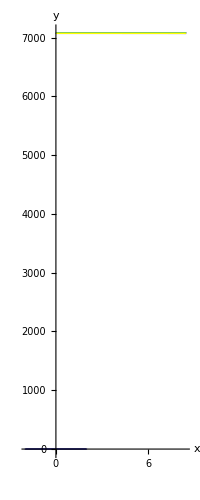

```mathematica
M=1;ivs={0,0,0};ics={0,12,π/2,Pi/4};
horizpl=PolarPlot[2,{θ,0,2 Pi},DisplayFunction->Identity];
a=.;
genPlot[mτ_,ain_,hue_]:=Block[{a,xyz},a=ain;
xyz=sphslnToCartsln[computeSoln[mτ,ivs,ics]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,mτ},DisplayFunction->Identity,PlotStyle->Hue[hue]]]
Table[genPlot[44.7,i M,1-i*(5/6)],{i,0,1,.2}];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y}]
```

Here the colors from red up to yellow are a/M=0,.2,.4,.6,.8, and 1, and the black circle is the Schwarzschild radius r= 2 M.  we see the behavior of an increasing value of a for a Kerr black hole: it causes increasing deflection of the particles in the same direction as the black hole rotates.

Another topic to examine is that of orbits that are counterrotating with respect to the black hole.  We will generate two orbits for the parameter sets, one corotating (in green) and another counterrotating (blue). We will look at the a/M=0 and a/M=0.9 cases and compare.

```mathematica
Clear[mτ,iv,ain,genPlot]
ccrPlot[mτ_,rin_,iv_,ain_]:=Block[{hpl,p1,p2,a},a=ain;ics={0,rin,π/2,Pi/4};
hpl=PolarPlot[M+Sqrt[M^2-ain^2],{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->Hue[0]];
xyzcor=sphslnToCartsln[computeSoln[mτ,{0,0,iv},ics]];
xyzcount=sphslnToCartsln[computeSoln[mτ,{0,0,-iv},ics]];
p1=ParametricPlot[Evaluate[{xyzcor[[1]],xyzcor[[2]]}//Flatten],{τ,0,mτ},DisplayFunction->Identity,PlotStyle->Hue[0.33]];
p2=ParametricPlot[Evaluate[{xyzcount[[1]],xyzcount[[2]]}//Flatten],{τ,0,mτ},DisplayFunction->Identity,PlotStyle->Hue[0.66]];
Show[p1,p2,hpl,DisplayFunction->$DisplayFunction,PlotLabel->"a="<>ToString[a]]]
ccrPlot[1000,10,.045,0];
ccrPlot[1000,10,.045,0.9 M];
```

These two plots show the general pattern: corotating orbits are boosted by the rotation, while the counterrotating orbits are sapped. There is also a broken symmetry- in the Schwarzschild case, the corotating and counterrotating orbits are exact mirrors of each other, while including a Kerr parameter quickly results in orbits that barely resemble each other. One other interesting case below illustrates this effect further - for the right choice of parameters, the corotating particle can maintain a stable orbit while the counterrotating one falls into the horizon.

```mathematica
ccrPlot[60.5,10,.034,0.5];
```

Now we will look at more complicated orbits in 3 dimensions for a Kerr black hole near the a/M=1 limit.  The initial coonditions are set to provide velocities in all 3 coordinates so as to allow for a more complicated orbit.  Note that the sphere and red circles here no longer correspend to the Schwarzschild radius, but instead the r_+=M-√(M^2-a^2)from Hartle (15.6) .

```mathematica
maxτ=500;M=1;a=0.99;rplus=M+Sqrt[M^2-a^2];
soln=computeSoln[maxτ,{-0.01,0.01,0.017},{0,10,π/3,Pi/4}];
xyzsoln=sphslnToCartsln[soln];
Plot[Evaluate[Table[coords[[i]][τ]/.soln,{i,1,n}]],{τ,0,maxτ},PlotStyle->Table[Hue[(i-1)/n],{i,1,n}],PlotLegend->coords,LegendPosition->{1,-.35},AxesLabel->{"τ","Coordinate"}];
SphericalPlot3D[{rplus,EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity];
ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotPoints->500]
Show[%,%%,DisplayFunction->$DisplayFunction];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},PlotStyle->Hue[0],DisplayFunction->Identity];
ParametricPlot[Evaluate[Re[{xyzsoln[[1]],xyzsoln[[2]]}]//Flatten],{τ,0,maxτ},AspectRatio->1,AxesLabel->{x,y},DisplayFunction->Identity];
Show[%,horizpl,DisplayFunction->$DisplayFunction];
ParametricPlot[Evaluate[Re[{xyzsoln[[2]],xyzsoln[[3]]}]//Flatten],{τ,0,maxτ},AxesLabel->{y,z},DisplayFunction->Identity];
Show[%,horizpl,DisplayFunction->$DisplayFunction];
ParametricPlot[Evaluate[Re[{xyzsoln[[1]],xyzsoln[[3]]}]//Flatten],{τ,0,maxτ},AxesLabel->{x,z},DisplayFunction->Identity];
Show[%,horizpl,DisplayFunction->$DisplayFunction,AspectRatio->1];
Join[{"Final Coordinates:"},coordlist[maxτ]]//TableForm
Join[{{"","","","u·u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

⁃Graphics3D⁃

Final Coordinates:
t = 651.421
r = 5.59662
θ = 1.16483
ϕ = 50.4904

|  |  | u·u values
τ= | 0 | → | -1.
τ= | 100 | → | -1.
τ= | 200 | → | -1.
τ= | 300 | → | -1.
τ= | 400 | → | -1.
τ= | 500 | → | -1.

Here we finally see orbits completely like anything at all familiar. By orbiting in a plane other than the equatorial plane, the rotational effects of the black hole pull the orbit into a shape that has no obvious symmetry properties, unlike the Schwarzschild case, where the coordinate system could always be re-oriented to lie in a plane.  Despite these oddities, the time dilation is not too extreme (~1.3), and u·u stays very close to -1, so this orbit is indeed the free-fall orbit in the Kerr geometry.  Below are a few other interesting orbits for various other initial conditions.

One final situation to investigate is that of light-ray orbits in the Kerr Geometry.  This can be accomplished simply by setting u·u=0 instead of -1.

```mathematica
uinvar=0;
maxτ=200;M=1;a=0.9;rplus=M+Sqrt[M^2-a^2];
horizpl=PolarPlot[M+Sqrt[M^2-a^2],{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->Hue[0]];
soln=computeSoln[maxτ,{-.15,0,.002},{0,10,π/2,Pi/4}];
xyzsoln=sphslnToCartsln[soln];
Plot[Evaluate[Table[coords[[i]][τ]/.soln,{i,1,n}]],{τ,0,maxτ},PlotStyle->Table[Hue[(i-1)/n],{i,1,n}],PlotLegend->coords,LegendPosition->{1,-.35},AxesLabel->{"τ","Coordinate"}];
ParametricPlot[Evaluate[{xyzsoln[[1]],xyzsoln[[2]]}//Flatten],{τ,0,maxτ},DisplayFunction->Identity];
Show[%,horizpl,DisplayFunction->$DisplayFunction,AspectRatio->1];
Join[{"Final Coordinates:"},coordlist[maxτ]]//TableForm
Join[{{"","","","u·u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

Final Coordinates:
t = 34.2151
r = 10.4087
θ = 1.5708
ϕ = 9.32262

|  |  | u·u values
τ= | 0 | → | -2.1684×10^-18
τ= | 40 | → | 2.24134×10^-8
τ= | 80 | → | 1.06117×10^-8
τ= | 120 | → | 5.57605×10^-9
τ= | 160 | → | 1.33473×10^-8
τ= | 200 | → | 1.38397×10^-8

Here we see an example light ray path that circles around the black hole, almost falling in but escapint to travel in roughly the same path it begin.  Very odd optical effects must exist near the surface of black holes... Also, note that the parameter τ is now an affine parameter instead of a proper time (meaningless for a light ray), although the coordinates still hold their ordinary meaning.   the u·u values also show that the orbit remains very close to that expected for a light ray (which should have u·u=0), although not exactly so out to the 8th decimal place in the dx_i/dτ.
An even more interesting example is that of light rays with corotating and counterrotating orbits.

```mathematica
ccrPlot[100,5,.12,0.5];
```

The effect here is that a flashbulb going off near a Kerr black hole will result in a highly anisotropic light pattern, strengthened in the direction of rotation and weakened in the counterrotating direction. One final interesting result is a light ray path falling into the black hole that gets caught by the rotatio near the pole and is forced to spiral in - it is facinating to imagine what the radiation patterns might look like.

```mathematica
maxτ=12;M=1;a=0.99;
xyzsoln=sphslnToCartsln[computeSoln[maxτ,{-.5,0,-.02},{0,7,π/3,Pi/4}]];
SphericalPlot3D[{M+Sqrt[M^2-a^2],EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity];
ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotPoints->300];
Show[%,%%,DisplayFunction->$DisplayFunction,ViewPoint->{-1,-1,1}];
```

```mathematica
Conclusion
```

We've examined a wide variety of orbits (both of particles and light rays) in the Kerr geometry.  The initial "experimental" goal was ahieved - early we recognized that the Kerr rotational effects are not strong enough to produce any perturbation on Mercury that would not be swamped by the Schwarzschild rotation.  Much more interesting are some of the unusual, highly asymmetric orbits that arise from Kerr geometry, particularly for light rays, which normally have relatively simple paths in the absence of interactions with charged materials.  A fascinating (but probably much more complicated) follow-on to this project would be that of determining optical effects from the Kerr geometry by ray-tracing or some similar such technique.  At any event however, the feasability of this method to compute orbits has been confirmed - analytic expected results were recovered, and u·u was mostly stable near its correct value.